```mathematica
rtColor=RGBColor[0.29,0.75,0.19];
lfColor=RGBColor[0.93,0.69,0.32];
mainColor=RGBColor[0.23,0.58,0.93];

total=7;
rt =Length[Ids];
lf = rt-1;

Ids = Table[i,{i,total}];
Ins:= Table[If[i<4,1,0],{i,total}];
Rects := Table[Rectangle[{Ids[[i]],0}],{i,total}];
Texts := Table[Text[Style[Ins[[i]],Large,mainColor,FontFamily->"Consolas"] ,{Ids[[i]] + 0.5,0.5}],{i,total}];

Arrows:={Thick,lfColor,Arrow[{{Ids[[lf]] + 0.5,-.75},{Ids[[lf]] + 0.5,0}}],rtColor,Arrow[{{Ids[[rt]] + 0.5,-.75},{Ids[[rt]] + 0.5,0}}]}
CurrentRects:={Opacity[0.2],mainColor,Rects[[Ids[[lf]]]],Rects[[Ids[[rt]]]]}
```

```mathematica
G := Graphics[Arrows~Join~{Black}~Join~Texts~Join~{EdgeForm[Directive[Thick,mainColor]],Transparent}~Join~Rects~Join~CurrentRects,ImageSize->Medium]
```

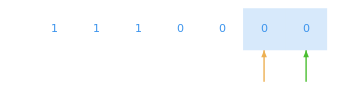

```mathematica
G
```